```mathematica
f[x_,u_,sigma_]:= 1/(Sqrt[2Pi sigma^2])Exp[-(x-u)^2/(2sigma^2)]
g[x_,u_,sigma_]:=1/2(1 + Erf[(x-u)/(Sqrt[2 sigma^2])])
```

```mathematica
f[x_,k_,theta_]:= 1/(Gamma[k]theta^k)x^(k-1)Exp[-x/theta]
g[x_,k_,theta_]:=1/Gamma[k]
```

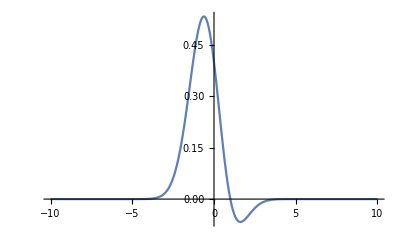

```mathematica
Plot[(D[f[x,0,1],x]+D[g[x,0,1],x])//Evaluate,{x,-10,10},PlotRange->All]
```

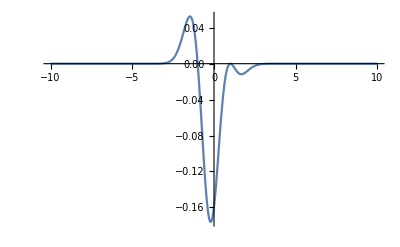

```mathematica
Plot[((D[f[x,0,1],x]+D[g[x,0,1],x])(D[f[x,0,1],{x,2}]))/.x->y,{y,-10,10},PlotRange->All]
```

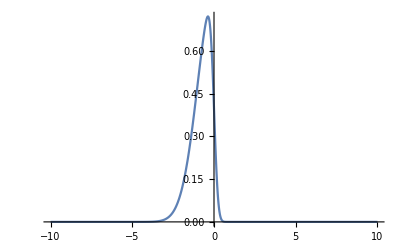

```mathematica
Plot[PDF[SkewNormalDistribution[0,1,-5],x],{x,-10,10},PlotRange->All]
```

```mathematica
NIntegrate[(D[PDF[SkewNormalDistribution[0,1,1],x],x]D[PDF[SkewNormalDistribution[0,1,1],x],{x,2}])//Evaluate,{x,-10,10},Method->"LocalAdaptive"]
```

-1.92839×10^-15

```mathematica
Manipulate[Plot[(D[PDF[SkewNormalDistribution[0,2,alpha],x],x]D[PDF[SkewNormalDistribution[0,2,alpha],x],{x,2}])//Evaluate,{x,-10,10},PlotRange->All],{alpha,-5,5}]
```